## General

```mathematica
Clear["`*"]
```

```mathematica
home =NotebookDirectory[]
```

```mathematica
export = False;
exportResult = False;
```

```mathematica
colorsPlots = {
bacteria -> Red,
food -> Blue,
highgrowth -> Brown,
highaffinity-> Purple
};
```

### Functions

```mathematica
Options@FindRoots=Sort@Join[Options@FindRoot,{MaxRecursion->Automatic,PerformanceGoal:>$PerformanceGoal,PlotPoints->Automatic,Debug->False,ZeroTolerance->10^-2}];

FindRoots[fun_,{var_,min_,max_},opts:OptionsPattern[]]:=Module[{PlotRules,RootRules,g,g2,pts,pts2,lpts,F,sol},(*Extract the Options*)PlotRules=Sequence@@FilterRules[Join[{opts},Options@FindRoots],Options@Plot];
RootRules=Sequence@@FilterRules[Join[{opts},Options@FindRoots],Options@FindRoot];
(*Plot the function and "mesh" the point with y-coordinate 0*)g=Normal@Plot[fun,{var,min,max},MeshFunctions->(#2&),Mesh->{{0}},Method->Automatic,Evaluate@PlotRules];
(*Get the meshes zeros*)pts=Cases[g,Point[p_]:>SetPrecision[p[[1]],OptionValue@WorkingPrecision],Infinity];
(*Get all plot points*)lpts=Join@@Cases[g,Line[p_]:>SetPrecision[p,OptionValue@WorkingPrecision],Infinity];
(*Derive the interpolated data to find other zeros*)F=Interpolation[lpts,InterpolationOrder->2];
g2=Normal@Plot[Evaluate@D[F@var,var],{var,min,max},MeshFunctions->(#2&),Mesh->{{0}},Method->Automatic,Evaluate@PlotRules];
(*Get the meshes zeros and retain only small ones*)pts2=Cases[g2,Point[p_]:>SetPrecision[p[[1]],OptionValue@WorkingPrecision],Infinity];
pts2=Select[pts2,Abs[F@#]<OptionValue@ZeroTolerance&];
pts=Join[pts,pts2];(*Join all zeros*)(*Refine zeros by passing each point through FindRoot*)If[Length@pts>0,pts=Map[FindRoot[fun,{var,#},Evaluate@RootRules]&,pts];
sol=Union@Select[pts,min≤Last@Last@#≤max&];
(*For debug purposes*)If[OptionValue@Debug,Print@Show[g,Graphics@{PointSize@0.02,Red,Point[{var,fun}/.sol]}]];
sol,If[OptionValue@Debug,Print@g];
{}]]
```

### Equations

#### Selection coefficient

s = species
m = metabolite
extra* or here s = mutant

The selection co-efficient of a mutant (with ks and mus) in a population of resident (with k and mu)

```mathematica
selectionCoeff = Log[((ks + m0)/ks)^(mus/mu(k-ks)/(ks + s0/y + m0))((s0 + y m0)/s0)^(mus/mu(k+ s0/y +m0)/(ks+ s0/y +m0))]/Log[((s0 + y m0)/s0) ]
```

Log[((ks+m0)/ks)^(((k-ks) mus)/(mu (ks+m0+s0/y))) ((s0+m0 y)/s0)^((mus (k+m0+s0/y))/(mu (ks+m0+s0/y)))]/Log[(s0+m0 y)/s0]

Same as above, but then for 1/ks (ksrec), for plotting (such that higher values are “better”)

```mathematica
selectionCoeffRec = selectionCoeff/. ks-> 1/ksrec
```

Log[(ksrec (1/ksrec+m0))^(((k-1/ksrec) mus)/(mu (1/ksrec+m0+s0/y))) ((s0+m0 y)/s0)^((mus (k+m0+s0/y))/(mu (1/ksrec+m0+s0/y)))]/Log[(s0+m0 y)/s0]

```mathematica
growthFactor = ((ks + m0)/ks)^(mus/mu(k-ks)/(ks + s0/y + m0))((s0 + y m0)/s0)^(mus/mu(k+ s0/y +m0)/(ks+ s0/y +m0))
```

((ks+m0)/ks)^(((k-ks) mus)/(mu (ks+m0+s0/y))) ((s0+m0 y)/s0)^((mus (k+m0+s0/y))/(mu (ks+m0+s0/y)))

#### The selection coefficient if the substrate does not run out completely

```mathematica
selectionCoeffFast = Log[((ks + m0)/(ks+me))^(mus/mu(k-ks)/(ks + s0/y + m0))((s0 + y (m0-me))/s0)^(mus/mu(k+ s0/y +m0)/(ks+ s0/y +m0))]/Log[((s0 + y (m0-me))/s0) ]
```

Log[((ks+m0)/(ks+me))^(((k-ks) mus)/(mu (ks+m0+s0/y))) ((s0+(m0-me) y)/s0)^((mus (k+m0+s0/y))/(mu (ks+m0+s0/y)))]/Log[(s0+(m0-me) y)/s0]

### Parameters

#### Plot parameters

```mathematica
colorIF = .5;
colorIncr1 = .2;
colorIncr2 = .6;
```

```mathematica
contourincr = .1;
```

```mathematica
tradeoffColor = White;
residentColor = Cyan;
```

#### Lenski experiment

Values in:
(m0 / k) mM for glucose
(s0 / sFinal) gram/liter for cells
(mu) h^-1 for growth rate
 (y) g cells / mmol glucose for yield

```mathematica
weightMolGlucose = 180 (*gram*);
```

```mathematica
valuesLenski = {
initGlucose -> 25 (* mg/L (μg/mL) *),
statPhase -> 5* 10^7 (*cells per ml*),
cellWeight -> 0.95(*picogram per cell (bionumbers - wetweight)*),
sFinal -> statPhase * cellWeight * 10^(-12)(*picogram to gram*)*10^3(*ml to l*)
};
```

```mathematica
paramLenski = {
m0 -> 0.99 (*1% is old culture without nutrients*)*initGlucose/weightMolGlucose (*mM*),
s0-> sFinal* 10^-2(*transfers are 0.1 ml on 10 ml culture*) (*g/L*)
};
```

```mathematica
paramLenski2 = {
y -> (sFinal - s0)/m0(*(g/L)/mM*)
};
```

```mathematica
resParam = {
mu -> .7726 (*h^-1*),
k -> .0727 (*μg / ml*)/weightMolGlucose  (*naar mM*)
}
```

{mu→0.7726,k→0.000403889}

```mathematica
paramLenskiFinal = Join[paramLenski, paramLenski2/. paramLenski]//. valuesLenski;
```

```mathematica
paramLenskiFinal//N
```

{m0→0.1375,s0→0.000475,y→0.342}

Values in:
(m0 / k) mg/L for glucose
(s0 / sFinal) cells/liter for cells
 (y) cells / mg glucose for yield

```mathematica
valuesLenskiOrigUnits = {
m0 -> 0.99 * initGlucose (*mg/L*),
s0 -> statPhase * 10^3 * 10^(-2) (*cells per L*)
}/. valuesLenski;
```

```mathematica
paramLenskiOrigUnits = {
y -> (statPhase * 10^3 - s0)/m0(*cells/mg*)
}/. valuesLenskiOrigUnits/.valuesLenski ;
```

```mathematica
measyield = {
y-> 2.6352 *10^6 (*cells/microg*)
};
```

```mathematica
valuesLenskiMeasYield = {
m0 -> 0.99 * initGlucose * 10^(3) (*microg/L*),
s0 -> 0.01 * y * initGlucose* 10^(3) (*cells per L*)
}/. measyield/. valuesLenski;
```

```mathematica
2.6352 *10^6(*cells/microg*)*weightMolGlucose (*cells/micromol*)*10^3(*cells/millimol*)
```

4.74336×10^11

#### Other

```mathematica
lowGlucosePar = paramLenskiFinal/. Rule[m0, x_]:>Rule[m0, x/100]
```

{m0→0.001375,s0→0.000475,y→0.342}

```mathematica
highGlucosePar = paramLenskiFinal/. Rule[m0, x_]:>Rule[m0, x*100]
```

{m0→13.75,s0→0.000475,y→0.342}

## Trade-off between mu and k (Appendix Figure A.1 and A.2 Left and Middle panel)

Artificial Trade-Off:
mumaxToyModel[k]

Plos comp anaerobic conditions:
mumaxPCanae[k]

Plos comp aerobic conditions:
mumaxPCae[k]

Wirtz:
mumaxWirtz[k]

Yeast:
mumaxYeast[k]

### Wirtz2002

The problem here is that the parameters they give in the paper do not match with the trade-off line they plot in the paper.

I will use the values that I have refitted, they correspond to the line shown in the paper, but then I will rescale the kStar to be in mM (paramWirtz).

This is what I will use later in the document:

tradeoffWirtz
paramWirtz
(tradeoffWirtzRec with krec ipv k (krec = 1/k))
mumaxWirtz[k]

```mathematica
paramWirtzOrig = {muStar-> 1.35 (*h^-1*), kStar-> 5.5 (*μg L^-1*)};
```

```mathematica
paramWirtzAdjRho = {muStar-> 1.35 - 0.12 (*h^-1*), kStar-> 5.5 (*μg L^-1*)};
```

```mathematica
tradeoffWirtz= {mu-> muStar Log[k/kStar]/(Log[k/kStar]+1)};
```

```mathematica
tradeoffWirtzRec = tradeoffWirtz/. {k-> 1/krec};
```

```mathematica
mu/.tradeoffWirtz/.paramWirtzOrig/. k-> 100
```

1.00388

```mathematica
wirtzSquares = Import[home<>"data\\WirtzSquares.csv"]⟦2;;⟧;
wirtzClosedCircles = Import[home<>"data\\WirtzClosedCircles.csv"]⟦2;;⟧;
wirtzOpenCircles = Import[home<>"data\\WirtzOpenCircles.csv"]⟦2;;⟧;
wirtzTradeoffLine = Import[home<>"data\\WirtzTradeoffLine.csv"]⟦2;;⟧;
```

```mathematica
wirtzData = ListLogLinearPlot[{wirtzSquares, wirtzClosedCircles, wirtzOpenCircles, wirtzTradeoffLine}, Joined-> {False, False, False, True}, PlotRange->{0.4, 1.4}, PlotMarkers-> {□,●,○,""}, PlotLegends->{"data","data","data","Trade-off line according to paper"}, AxesLabel->{"mu (h-1)", "k (microg/L)"}]
```

-Graphics-

```mathematica
wirtzFit =NonlinearModelFit[wirtzTradeoffLine,mu/.tradeoffWirtz, {muStar, kStar}, k]
```

FittedModel[(1.21424 Log[0.156631 k])/(1+Log[0.156631 k])]

```mathematica
wirtzFit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
muStar | 1.21424 | 0.00115165 | 1054.36 | 3.59805×10^-72
kStar | 6.38444 | 0.0295088 | 216.357 | 7.48548×10^-51

```mathematica
wirtzFit2 =NonlinearModelFit[wirtzTradeoffLine,mu/.tradeoffWirtz/. kStar-> 5.5, {muStar}, k]
```

FittedModel[(1.19715 Log[0.181818 k])/(1+Log[0.181818 k])]

```mathematica
wirtzFit2["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
muStar | 1.19715 | 0.00527243 | 227.058 | 6.72714×10^-53

```mathematica
wirtzFit3 =NonlinearModelFit[wirtzTradeoffLine,mu/.tradeoffWirtz/. muStar-> 1.35, {kStar}, k]
```

FittedModel[(1.35 Log[0.128986 k])/(1+Log[0.128986 k])]

```mathematica
wirtzFit3["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
kStar | 7.75276 | 0.474743 | 16.3304 | 4.44723×10^-17

```mathematica
paramWirtzFit= wirtzFit["BestFitParameters"];
paramWirtzFitMu = Join[{kStar-> 5.5 (*μg L^-1*)}, wirtzFit2["BestFitParameters"]];
paramWirtzFitK = Join[{muStar-> 1.35 (*h^-1*)}, wirtzFit3["BestFitParameters"]];
paramWirtz = paramWirtzAdjRho/. Rule[kStar, val_]:> Rule[kStar, (val/1000)/weightMolGlucose ] (*kStar converted to mM*)
```

{muStar→1.23,kStar→0.0000305556}

```mathematica
wirtzSim = LogLinearPlot[{mu/.tradeoffWirtz/.paramWirtzOrig, mu/.tradeoffWirtz/.paramWirtzAdjRho}, {k, 10, 100000}, PlotRange->{0.4, 1.4}, PlotLegends->{"Replotted from paper", "Replotted  - adj Rho"}];
Show[wirtzData, wirtzSim]
```

-Graphics-

```mathematica
wirtzSimFit = LogLinearPlot[mu/.tradeoffWirtz/.paramWirtzFit, {k, 10, 100000}, PlotRange->{0.4, 1.4}, PlotLegends->"Trade-off line refitted (so with different parameter values)"];
Show[wirtzData, wirtzSimFit]
```

-Graphics-

```mathematica
wirtzSimFitMu = LogLinearPlot[mu/.tradeoffWirtz/.paramWirtzFitMu, {k, 10, 100000}, PlotRange->{0.4, 1.4}, PlotLegends->"Trade-off line with only mu refitted"];
Show[wirtzData, wirtzSimFitMu]
```

-Graphics-

```mathematica
wirtzSimFitK = LogLinearPlot[mu/.tradeoffWirtz/.paramWirtzFitK, {k, 10, 100000}, PlotRange->{0.4, 1.4}, PlotLegends->"Trade-off line with only k refitted"];
Show[wirtzData, wirtzSimFitK]
```

-Graphics-

```mathematica
mumaxWirtz[kinput_]:= mu/. tradeoffWirtz/. paramWirtz/. k-> kinput
```

### Plos Comp paper - Aerobic (Appendix Figure A.1 Left and Middle Panel)

What I use from this is the function mumaxPCae[k] that takes a k and gives a mumax.

```mathematica
dataNew=Import[home<>"data//monod_params.xls"];
```

```mathematica
dataPlot = Reverse/@dataNew[[1, 2;;,{2,3}]];
paretoAerobic=Internal`ListMin[dataPlot /. {k_, mu_}:> {k, 1/mu}]/. {k_, mu_}:> {k, 1/mu};
dataPlotRec = dataPlot/. {k_, mu_}:> {1/k, mu};
```

```mathematica
paretoPos = Flatten[Position[dataPlot⟦All,1⟧, #]&/@paretoAerobic⟦All,1⟧, Infinity];
```

```mathematica
Total[Complement[paretoAerobic,dataPlot[[paretoPos]]]-Complement[dataPlot[[paretoPos]], paretoAerobic]](*check for the paretoPos: this should be 0*)
```

{0.,-2.60209×10^-17}

This yield is per mmol C -> should be converted to glucose (multiply by 6)
This yield is in mgDW / mmol C/Glu, should be converted to 10^9 cells/mmol Glu
1 cell is 0.28 pg (Neidhardt) = 0.28*10^-9 mg so should be divided by this, then divided by 10^9 => divided by 0.28

```mathematica
dataGrowthYield = dataNew[[1, 2;;,{2,6}]];
```

```mathematica
dataGrowthYieldGlu = dataGrowthYield/. {mu_, y_}:> {mu, y*6/0.28};
```

```mathematica
fitGrowthYieldData =NonlinearModelFit[dataGrowthYieldGlu⟦paretoPos⟧,{ (maxY*mu)/(mu+kY), maxY>0, kY>0}, {maxY, kY},mu]
```

FittedModel[(495.01 mu)/(0.0725938+mu)]

```mathematica
fitGrowthYield[mu_]:= (maxY*mu)/(mu+kY)/. {maxY -> 495, kY-> 7.26*10^(-2)}
```

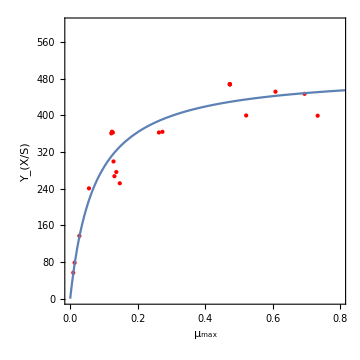

```mathematica
Show[ListPlot[dataGrowthYieldGlu⟦paretoPos⟧, Frame -> True,FrameLabel->{"μ_max", "Y_(X/S)"}, AspectRatio->1, PlotStyle-> {{PointSize[Medium], Red}}, BaseStyle->{16,FontFamily->"Arial"}, ImageSize->Medium, PlotRange-> {{0, 0.8},{0,600}}], Plot[fitGrowthYield[mu], {mu, 0, 1}, PlotRange-> All]]
```

```mathematica
tradeoffPlot = ListPlot[dataPlot, Frame -> True,FrameLabel->{"k_Monod", "μ"}, AspectRatio->1, PlotStyle-> {tradeoffColor,PointSize[Medium]}, BaseStyle->{16,FontFamily->"Arial"}, ImageSize->Medium];
```

```mathematica
tradeoffPlotRec = ListPlot[dataPlotRec, Frame -> True,FrameLabel->{"k_Monod", "μ"}, AspectRatio->1, PlotStyle-> {tradeoffColor,PointSize[Medium]}, BaseStyle->{16,FontFamily->"Arial"}, ImageSize->Medium];
```

```mathematica
mumaxPCae2 =NonlinearModelFit[paretoAerobic,{ tradeoffPlosComp, km>0, n>0}, {km, n},k]
```

NonlinearModelFit[{{0.00481588,0.733221},{0.00389514,0.694383},{0.00371654,0.608198},{0.00287896,0.521397},{0.00254176,0.473378},{0.00254005,0.473165},{0.00253966,0.473106},{0.00253025,0.472578},{0.00244617,0.273378},{0.00238553,0.262925},{0.00153263,0.146858},{0.00139109,0.136623},{0.00137496,0.131035},{0.00113812,0.128318},{0.000841456,0.126382},{0.000840683,0.123735},{0.000840143,0.121758},{0.000789843,0.0555384},{0.000758172,0.0271336},{0.000454546,0.0130684},{0.00042953,0.00908955}},{tradeoffPlosComp,km>0,n>0},{km,n},k]

```mathematica
paramsPlosCompAerobic =mumaxPCae2["BestFitParameters"]
```

NonlinearModelFit[{{0.00481588,0.733221},{0.00389514,0.694383},{0.00371654,0.608198},{0.00287896,0.521397},{0.00254176,0.473378},{0.00254005,0.473165},{0.00253966,0.473106},{0.00253025,0.472578},{0.00244617,0.273378},{0.00238553,0.262925},{0.00153263,0.146858},{0.00139109,0.136623},{0.00137496,0.131035},{0.00113812,0.128318},{0.000841456,0.126382},{0.000840683,0.123735},{0.000840143,0.121758},{0.000789843,0.0555384},{0.000758172,0.0271336},{0.000454546,0.0130684},{0.00042953,0.00908955}},{tradeoffPlosComp,km>0,n>0},{km,n},k][BestFitParameters]

```mathematica
mumaxPCae[k_] := (0.8 km^n)/((1/k)^n+km^n)/. km-> 417 /. n-> 2.7;
```

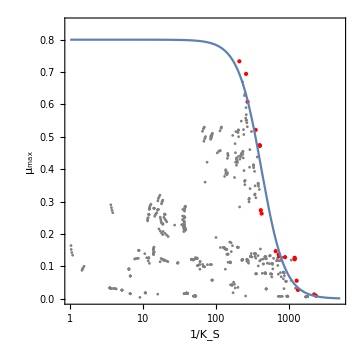

```mathematica
Show[ListLogLinearPlot[{dataPlotRec,paretoAerobic/. {k_, mu_}:> {1/k, mu}}, Frame -> True,FrameLabel->{"1/K_S", "μ_max"}, AspectRatio->1, PlotStyle-> {Gray,{PointSize[Medium], Red}}, BaseStyle->{16,FontFamily->"Arial"}, ImageSize->Medium, PlotRange-> {{1, 5000},{0,0.85}}], LogLinearPlot[mumaxPCae[1/x], {x, 1, 5000}]]
```

### Plos Comp paper - Anaerobic (Appendix Figure A.1 Right Panel)

What I use from this is the function mumaxPCanae[k] that takes a k and gives a mumax.

```mathematica
dataNew=Import[home<>"data//monod_params.xls"];
```

```mathematica
dataPlotAnaerobic = Reverse/@dataNew[[2, 2;;,{2,3}]];
paretoAnaerobic=Internal`ListMin[dataPlotAnaerobic /. {k_, mu_}:> {k, 1/mu}]/. {k_, mu_}:> {k, 1/mu};
dataPlotAnaerobicRec = dataPlotAnaerobic/. {k_, mu_}:> {1/k, mu};
```

```mathematica
tradeoffPlotAnaerobic = ListPlot[dataPlotAnaerobic, Frame -> True,FrameLabel->{"k_Monod", "μ"}, AspectRatio->1, PlotStyle-> {tradeoffColor,PointSize[Medium]}, BaseStyle->{16,FontFamily->"Arial"}, ImageSize->Medium];
```

```mathematica
paretoPosAnae = Flatten[Position[dataPlotAnaerobic⟦All,1⟧, #]&/@paretoAnaerobic⟦All,1⟧, Infinity];
```

```mathematica
Total[Complement[paretoAnaerobic,dataPlotAnaerobic[[paretoPosAnae]]]-Complement[dataPlotAnaerobic[[paretoPosAnae]], paretoAnaerobic]]
(*check for the paretoPos: this should be 0*)
```

{0.,-4.94396×10^-17}

This yield is per mmol C -> should be converted to glucose (multiply by 6)
This yield is in mgDW / mmol C/Glu, should be converted to 10^9 cells/mmol Glu
1 cell is 0.28 pg (Neidhardt) = 0.28*10^-9 mg so should be divided by this, then divided by 10^9 => divided by 0.28

```mathematica
dataGrowthYieldAnae = dataNew[[2, 2;;,{2,6}]];
```

```mathematica
dataGrowthYieldGluAnae = dataGrowthYieldAnae/. {mu_, y_}:> {mu, y*6/0.28};
```

```mathematica
fitGrowthYieldDataAnae =NonlinearModelFit[dataGrowthYieldGluAnae⟦paretoPosAnae⟧,{ (maxY*mu)/(mu+kY), maxY>0, kY>0}, {maxY, kY},mu]
```

FittedModel[(53.886 mu)/(0.+mu)]

```mathematica
fitGrowthYieldAnae[mu_]:= (maxY*mu)/(mu+kY)/. {maxY -> 495, kY-> 7.26*10^(-2)}
```

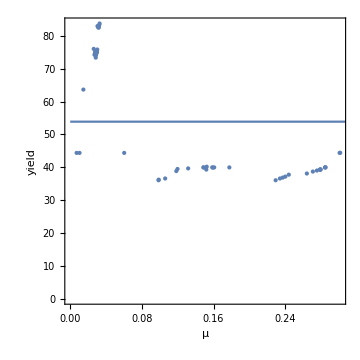

```mathematica
Show[ListPlot[dataGrowthYieldGluAnae⟦paretoPosAnae⟧, Frame -> True,FrameLabel->{"μ", "yield"}, AspectRatio->1, PlotStyle-> PointSize[Medium], BaseStyle->{16,FontFamily->"Arial"}, ImageSize->Medium], Plot[fitGrowthYieldDataAnae[mu],{mu,0,0.8}, PlotRange->All]]
```

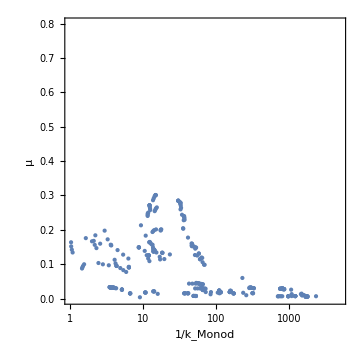
{-Graphics-,-Graphics-}

```mathematica
{ListLogLinearPlot[dataPlotAnaerobicRec, Frame -> True,FrameLabel->{"1/k_Monod", "μ"}, AspectRatio->1, PlotStyle-> {PointSize[Medium]}, BaseStyle->{16,FontFamily->"Arial"}, ImageSize->Medium, PlotRange-> {{1, 5000},{0,0.8}}], -Graphics-}
```

```mathematica
mumaxPCanae3 = NonlinearModelFit[paretoAnaerobic,{0.1 k/(k+kref1)+0.21 k^n/(kref2^n+ k^n), kref1>0,kref2>0,  n>0}, {kref1, kref2, n},k]
```

FittedModel[(0.1 k)/(0.00390067+k)+(0.21 k^(«18»))/(6.16996×10^-10+k^(«18»))]

```mathematica
mumaxPCanae3["BestFitParameters"]
```

{kref1→0.00390067,kref2→0.0230127,n→5.62243}

```mathematica
mumaxPCanae[k_]:=0.1 k/(kref1+k)+0.21 k^n/(kref2^n+ k^n)/. {kref1-> 3.9*10^(-3), kref2-> 2.3*10^(-2), n-> 5.6}
```

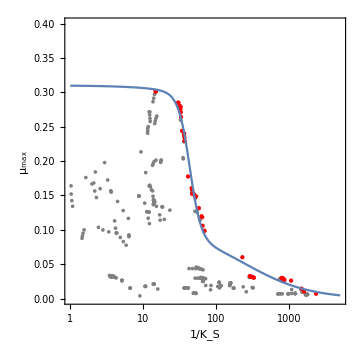

```mathematica
Show[ListLogLinearPlot[{dataPlotAnaerobicRec,paretoAnaerobic/. {k_, mu_}:> {1/k, mu}}, Frame -> True,FrameLabel->{"1/K_S", "μ_max"}, AspectRatio->1, PlotStyle-> {Gray,{PointSize[Medium], Red}}, BaseStyle->{16,FontFamily->"Arial"}, ImageSize->Medium, PlotRange-> {{1, 5000},{0,0.4}}], LogLinearPlot[{mumaxPCanae[1/x]}, {x, 1, 5000}]]
```

### Yeast Elbing fit (Appendix Figure A.2 Left and Middle panel)

```mathematica
mumaxElbing[k_]:=(0.34 k)/(0.77+k)
```

dry weight of S. cerevisiae = 15*10^(-12) gram (ref Sherman F. Getting started with yeast. Methods Enzymol. 2002 350: 3-41. p.15 table V PubMed ID 12073320)

Glucose consumption rate = 2-18 mmol Glu/gDW/h
Biomass production rate = 0.3 gDW/gDW /h
=> 10 mmol Glu is converted to 0.3 gDW = 0.3/15*10^(-12) cellen

```mathematica
(0.3/(15*10^(-12)))/10
```

2.×10^9

```mathematica
strains = {"Wild type", "HXT1", "TM12", "TM11", "HXT7", "TM1", "TM2", "TM3", "TM4", "TM5", "TM6"};
```

```mathematica
strainsGrowthRates = {0.35, 0.34, 0.35, 0.36, 0.34, 0.3, 0.3, 0.28, 0.26, 0.27, 0.23};
strainsParams = {{663, 76}, {806, 250}, {302, 44}, {522, 72}, {125, 2.5}, {73,4.6}, {113, 7}, {129, 6.2}, {103, 7.6}, {35, 4.9}, {61, 3.5}}
yields = {18, 14.5, 16, 16, 13, 5.5, 7.5, 6.2, 3.5, 3, 3.1};(*estimated from graph*)
yieldsElbing = yields/. {x_:> ((0.3/(15*10^(-12)))/x)/10^9}
```

{{663,76},{806,250},{302,44},{522,72},{125,2.5},{73,4.6},{113,7},{129,6.2},{103,7.6},{35,4.9},{61,3.5}}

{1.11111,1.37931,1.25,1.25,1.53846,3.63636,2.66667,3.22581,5.71429,6.66667,6.45161}

```mathematica
yieldElbingFitData = NonlinearModelFit[Transpose[{strainsGrowthRates, yieldsElbing}],{7 kY^n/(mu^n+kY^n), kY>0, n>0}, {kY, n},mu]
```

FittedModel[0.000026601/(3.80014×10^-6+mu^(«19»))]

```mathematica
yieldElbingFitData["BestFitParameters"]
```

{kY→0.297418,n→10.2922}

```mathematica
yieldElbingFit[mu_]:= 7 kY^n/(mu^n+kY^n)/. {kY-> 0.3, n-> 10}
```

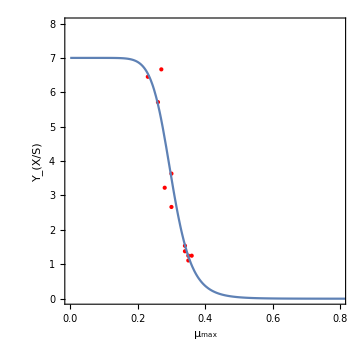

```mathematica
Show[ListPlot[Transpose[{strainsGrowthRates, yieldsElbing}], Frame -> True,FrameLabel->{"μ_max", "Y_(X/S)"}, AspectRatio->1, PlotStyle-> {{PointSize[Medium], Red}}, BaseStyle->{16,FontFamily->"Arial"}, ImageSize->Medium, PlotRange-> {{0, 0.8},{0,8}}], Plot[yieldElbingFit[mu], {mu, 0, 1}]]
```

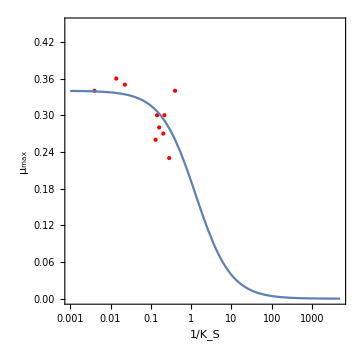

```mathematica
Show[ListLogLinearPlot[{Transpose[{strainsParams⟦2;;, 2⟧, strainsGrowthRates⟦2;;⟧}]/. {k_, mu_}:> {1/k, mu}}, Frame -> True,FrameLabel->{"1/K_S", "μ_max"}, AspectRatio->1, PlotStyle-> {{PointSize[Medium], Red}}, BaseStyle->{16,FontFamily->"Arial"}, ImageSize->Medium, PlotRange-> {{.001, 5000},{0,0.45}}], LogLinearPlot[mumaxElbing[1/x], {x, .001, 5000}]]
```

### Yeast ModelY fit

```mathematica
mumaxYeast[k_]:=(0.67 k)/(0.028+k)
```

Yield is fixed for resp or ferm: onder mumax=0.3 is het 0.117661
boven mumax=0.3 is het 0.0558889
gram biomass/millimol glucose
dry weight of S. cerevisiae = 15*10^(-12) gram

```mathematica
yieldResp = 0.117661/(15*10^(-12))*10^(-9)
```

7.84407

```mathematica
yieldFerm= 0.0558889/(15*10^(-12))*10^(-9)
```

3.72593

### Compare different trade-offs

Here I want to plot both the trade-offs from Wirtz and the Plos Comp paper to see how they compare.

```mathematica
tradeoffWirtz
```

{mu→(muStar Log[k/kStar])/(1+Log[k/kStar])}

```mathematica
paramWirtz
```

{muStar→1.23,kStar→0.0000305556}

```mathematica
3.056*10^-5
```

0.00003056

```mathematica
tradeoffPlosComp
```

tradeoffPlosComp

```mathematica
paramsPlosCompAerobic
```

NonlinearModelFit[{{0.00481588,0.733221},{0.00389514,0.694383},{0.00371654,0.608198},{0.00287896,0.521397},{0.00254176,0.473378},{0.00254005,0.473165},{0.00253966,0.473106},{0.00253025,0.472578},{0.00244617,0.273378},{0.00238553,0.262925},{0.00153263,0.146858},{0.00139109,0.136623},{0.00137496,0.131035},{0.00113812,0.128318},{0.000841456,0.126382},{0.000840683,0.123735},{0.000840143,0.121758},{0.000789843,0.0555384},{0.000758172,0.0271336},{0.000454546,0.0130684},{0.00042953,0.00908955}},{tradeoffPlosComp,km>0,n>0},{km,n},k][BestFitParameters]

```mathematica
mumaxYeast[km]
```

(0.67 km)/(0.028+km)

```mathematica
mumaxElbing[km]
```

(0.34 km)/(0.77+km)

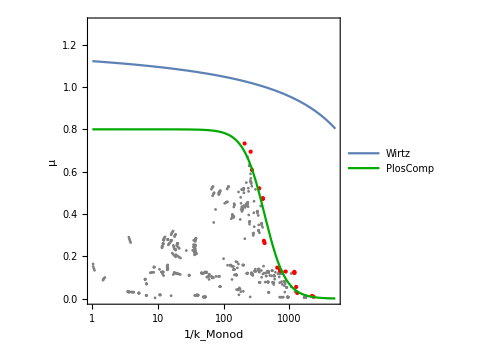

```mathematica
Show[ListLogLinearPlot[{dataPlotRec,paretoAerobic/. {k_, mu_}:> {1/k, mu}}, Frame -> True,FrameLabel->{"1/k_Monod", "μ"}, AspectRatio->1, PlotStyle-> {Gray,{PointSize[Medium], Red}}, BaseStyle->{16,FontFamily->"Arial"}, ImageSize->Medium, PlotRange-> {{1, 5000},{0,1.3}}],LogLinearPlot[mumaxWirtz[1/krec], {krec, 1, 5000}, PlotLegends->{"Wirtz"}],
LogLinearPlot[mumaxPCae[1/krec], {krec, 1, 5000}, PlotStyle->Darker[Green], PlotLegends->{"PlosComp"}]]
```

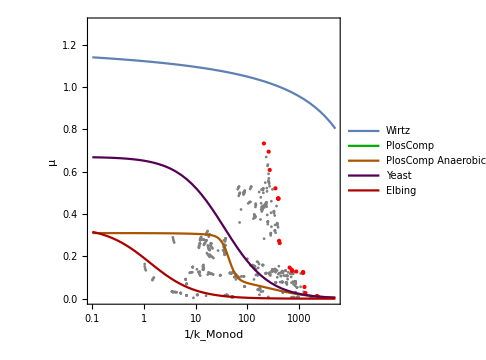

```mathematica
Show[ListLogLinearPlot[{dataPlotRec,paretoAerobic/. {k_, mu_}:> {1/k, mu}}, Frame -> True,FrameLabel->{"1/k_Monod", "μ"}, AspectRatio->1, PlotStyle-> {Gray,{PointSize[Medium], Red}}, BaseStyle->{16,FontFamily->"Arial"}, ImageSize->Medium, PlotRange-> {{.1, 5000},{0,1.3}}],LogLinearPlot[mumaxWirtz[1/krec], {krec, .1, 5000}, PlotLegends->{"Wirtz"}],
LogLinearPlot[mumaxPCae2[1/krec], {krec, .1, 5000}, PlotStyle->Darker[Green], PlotLegends->{"PlosComp"}],
LogLinearPlot[mumaxPCanae[1/krec], {krec, .1, 5000}, PlotStyle->Darker[Orange], PlotLegends->{"PlosComp Anaerobic"}],LogLinearPlot[mumaxYeast[1/krec], {krec, .1, 5000}, PlotStyle->Darker[Purple], PlotLegends->{"Yeast"}],
LogLinearPlot[mumaxElbing[1/krec], {krec, .1, 5000}, PlotStyle->Darker[Red], PlotLegends->{"Elbing"}]]
```

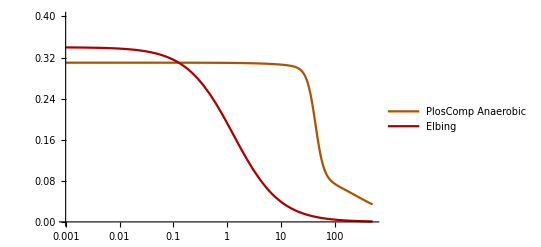

```mathematica
Show[
LogLinearPlot[mumaxPCanae[1/krec], {krec, .001, 500}, PlotStyle->Darker[Orange], PlotLegends->{"PlosComp Anaerobic"}, PlotRange->{0, 0.4}],
LogLinearPlot[mumaxElbing[1/krec], {krec, .001, 500}, PlotStyle->Darker[Red], PlotLegends->{"Elbing"}]
]
```

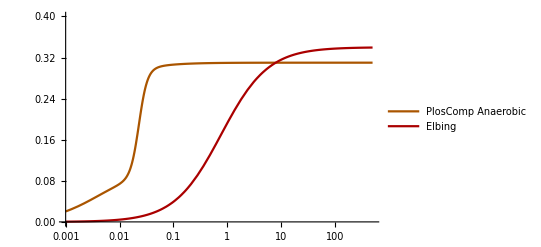

```mathematica
Show[
LogLinearPlot[mumaxPCanae[k], {k, .001, 500}, PlotStyle->Darker[Orange], PlotLegends->{"PlosComp Anaerobic"}, PlotRange->{0, 0.4}],
LogLinearPlot[mumaxElbing[k], {k, .001, 500}, PlotStyle->Darker[Red], PlotLegends->{"Elbing"}]
]
```

```mathematica
FindRoot[mumaxPCanae[k]==mumaxElbing[k], {k, 10}]
```

{k→7.94241}

```mathematica
krange = Table[1/krec, {krec, .1, 5000, .1}];
```

```mathematica
toplotWirtz =Table[{mumaxWirtz[k]/k, mumaxWirtz[k]}, {k, krange}];
toplotPCae =Table[{mumaxPCae[k]/k, mumaxPCae[k]}, {k, krange}];
toplotPCanae =Table[{mumaxPCanae[k]/k, mumaxPCanae[k]}, {k, krange}];
toplotYeast =Table[{mumaxYeast[k]/k, mumaxYeast[k]}, {k, krange}];
```

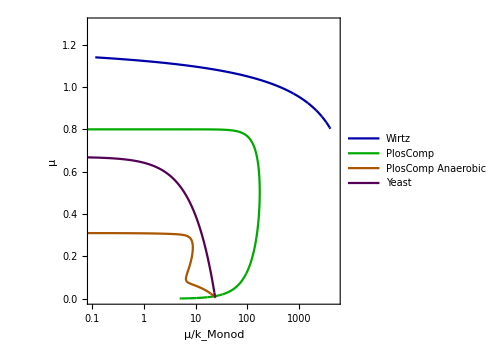

```mathematica
ListLogLinearPlot[{toplotWirtz, toplotPCae, toplotPCanae, toplotYeast}, Frame -> True,FrameLabel->{"μ/k_Monod", "μ"}, AspectRatio->1, Joined-> True,PlotStyle-> {Darker[Blue], Darker[Green], Darker[Orange], Darker[Purple], Darker[Yellow]},BaseStyle->{16,FontFamily->"Arial"}, PlotLegends->{"Wirtz", "PlosComp","PlosComp Anaerobic","Yeast"},ImageSize->Medium, PlotRange-> {{.1, 5000},{0,1.3}}]
```

## Analysis of the selection equation (Appendix Figure A.7)

```mathematica
paramLenskiFinal
```

{m0→0.1375,s0→0.000475,y→0.342}

```mathematica
lowGlucosePar
```

{m0→0.001375,s0→0.000475,y→0.342}

```mathematica
traitu[k_]:= Log10[(k/0.0001)]/Log10[(0.1/0.0001)]
kfromu[u_]:= 0.0001*10^(Log10[(0.1/0.0001)]*u)
```

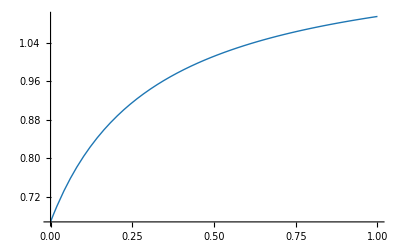

```mathematica
tradeoffLineWirtzU=Plot[mu/.tradeoffWirtz/.paramWirtz/. k-> kfromu[u], {u, 0, 1}, PlotRange->All, PlotStyle->{Thick,RGBColor["#1f77b4"]}];
tradeoffLineWirtzU
```

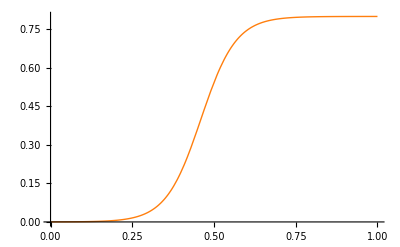

```mathematica
tradeoffLinePSaeU=Plot[mumaxPCae[kfromu[u]], {u, 0, 1}, PlotRange->All, PlotStyle->{Thick,RGBColor["#ff7f0e"]}];
tradeoffLinePSaeU
```

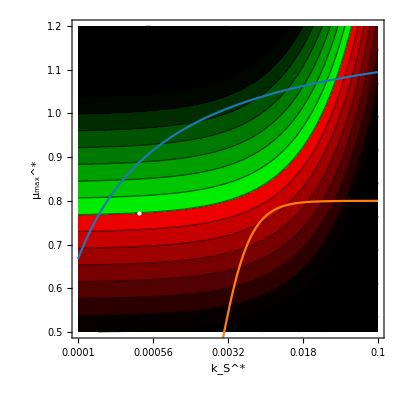

```mathematica
selCoeffNormalGlucose =Show[ContourPlot[selectionCoeff-1/. paramLenskiFinal/. resParam /. ks-> kfromu[u],  {u, 0, 1}, {mus, .5, 1.2},FrameLabel->{"k_S^*", "μ_max^*"},Contours-> Range[-1, 1, .05],
ColorFunctionScaling->False,
ColorFunction->(If[#>0,RGBColor[0,(1-3#),0],RGBColor[(3#+1),0,0]]&),
FrameTicks->{{Automatic, None}, {Transpose[{Range[0,1,.25], DecimalForm[#,2]&/@kfromu/@Range[0,1,.25]}], None}},
BaseStyle->{16,FontFamily->"Arial", FontColor-> Black},
PlotLegends->BarLegend[Automatic,LegendMarkerSize->180,LegendFunction->"Frame",LegendMargins->5,LegendLabel->"Selection coefficient"],Epilog-> {White,PointSize[Large],Point[{traitu[k], mu}/.  resParam]}], tradeoffLineWirtzU, tradeoffLinePSaeU]
```

```mathematica
(*Export[home<>"3. Analysed data\\figures\\selCoeffNormalGlucose.png", selCoeffNormalGlucose]*)
```

```mathematica
(*Export[home<>"3. Analysed data\\figures\\selCoeffNormalGlucose.pdf", selCoeffNormalGlucose]*)
```

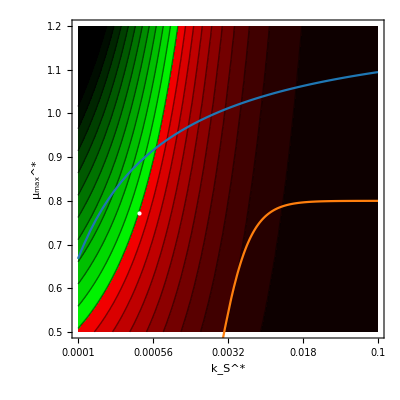

```mathematica
selCoeffLowGlucose=Show[ContourPlot[selectionCoeff-1/. lowGlucosePar/. resParam /. ks-> kfromu[u],  {u, 0, 1}, {mus, .5, 1.2},FrameLabel->{"k_S^*", "μ_max^*"},Contours-> Range[-1, 1, .1],
ColorFunctionScaling->False,
ColorFunction->(If[#>0,RGBColor[0,(1-#),0],RGBColor[(#+1),0,0]]&),
FrameTicks->{{Automatic, None}, {Transpose[{Range[0,1,.25], DecimalForm[#,2]&/@kfromu/@Range[0,1,.25]}], None}},
BaseStyle->{16,FontFamily->"Arial", FontColor-> Black},
PlotLegends->BarLegend[Automatic,LegendMarkerSize->180,LegendFunction->"Frame",LegendMargins->5,LegendLabel->"Selection coefficient"],Epilog-> {White,PointSize[Large],Point[{traitu[k], mu}/.  resParam]}], tradeoffLineWirtzU, tradeoffLinePSaeU]
```

```mathematica
(*Export[home<>"3. Analysed data\\figures\\selCoeffLowGlucose.png", selCoeffLowGlucose]*)
```

```mathematica
(*Export[home<>"3. Analysed data\\figures\\selCoeffLowGlucose.pdf", selCoeffLowGlucose]*)
```

## The selection gradient (Appendix Figure A.6)

As defined in Vasi et al.:

```mathematica
selK = (-k (1+ Log[(k+m0)/k]/Log[(s0 + y m0)/s0]))/(k+s0/y+m0)
```

-(k (1+Log[(k+m0)/k]/Log[(s0+m0 y)/s0]))/(k+m0+s0/y)

### Reproduce results from Vasi et al.

```mathematica
selK/. valuesLenskiOrigUnits /. paramLenskiOrigUnits/. k -> .0727
```

-0.00657233

Value from Vasi et al. paper is: -0.0066 -> Agrees!

```mathematica
selK/. paramLenskiFinal/. resParam
```

-0.00657233

In the new units it also matches.

### Analyse the selection gradient (Appendix Figure A.6)

#### Plot selection gradient of k in LTEE for different values of k

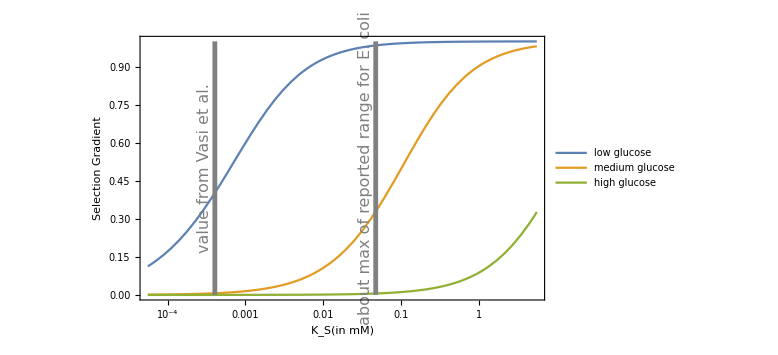

```mathematica
selGradientPlot = LogLinearPlot[{-selK/. lowGlucosePar, -selK/. paramLenskiFinal, -selK/. highGlucosePar}, {k, 0.01/weightMolGlucose,1000/weightMolGlucose }, PlotRange->All, BaseStyle->{18,FontFamily-> "Arial"}, Frame-> True,
FrameTicks->{{Automatic, None}, {Automatic, None}},
FrameLabel-> {"K_S(in mM)","Selection Gradient"},
ImageSize->Large,
Epilog->{Gray,Thickness[.006], Line[{{ Log[.0727/weightMolGlucose ], 0}, {Log[.0727/weightMolGlucose ], 1}}], Line[{{ Log[8.5/weightMolGlucose ], 0}, {Log[8.5/weightMolGlucose ], 1}}], Inset[Style["value from Vasi et al.", 16],{Log[.0727/weightMolGlucose ]-.3, 0.5}, Automatic, Automatic,{0, 1}], Inset[Style["about max of reported range for E. coli", 16],{Log[8.5/weightMolGlucose ]-.3, 0.5}, Automatic, Automatic,{0, 1}]}, PlotLegends->Placed[LineLegend[{"low glucose", "medium glucose", "high glucose"},LabelStyle->{14,FontFamily->"Arial"}],{{.7, .3}, {.1,.1}}]
]
```

```mathematica
(*Export[home<>"3. Analysed data\\figures\\selGradient.pdf",selGradientPlot]*)
```

```mathematica
(*Export[home<>"3. Analysed data\\figures\\selGradient.png",selGradientPlot]*)
```

## Ecological bistability

This shows that in principle, it is possible to have ecological bistability -> That the final outcome of the experiment depends on the initial ratio. The type that remains is the one that was originally present. This happens when a cannot invade in b and b cannot invade in a. Below some parameters that show this can happen. However, it does not happen for any parameters of the experimentally or computationally derived trade-offs.

s = species
m = metabolite
extra* or here s = mutant

The selection co - efficient of a mutant (with ks and mus) in a population of resident (with k and mu)

W(b-> a)

```mathematica
selectionCoeff /. {s0-> 10, m0-> 1, k-> .5, mu-> 5, ks-> .4, mus-> 4.5, y-> 100}
```

0.991347

W(a-> b)

```mathematica
selectionCoeff /. {s0-> 10, m0-> 1, ks-> .5, mus-> 5, k-> .4, mu-> 4.5, y-> 10}
```

0.996224

Try to find more realistic values

W(b-> a)

```mathematica
selectionCoeff /. {s0-> 0.1, m0-> 100, k-> 1.7, mu-> .92, ks-> .4, mus-> .9, y-> 10}
```

0.998524

W(a-> b)

```mathematica
selectionCoeff /. {s0-> 0.1, m0-> 100, ks-> 1.7, mus-> .92, k-> .4, mu-> .9, y-> .1}
```

0.997812